## Distribution Gassian: Energy_Reconstruction x Energy_True

README: Since we’re assuming a reconstruction of energy by a Gassian, it’s worth taking a moment to understand it better.

Reconstruction function (Gassian):

```mathematica
Clear[FuncGassian]
FuncGassian[Ere_,Etrue_]:=1/(σe*√(2*π))*Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}]            (* Gassian function *)
Clear[Fcut]
Fcut[Ere_,Etrue_]:=Piecewise[  {  { 0,Etrue<3.35 }  },  If[  FuncGassian[Ere,Etrue]<10^-5,0,FuncGassian[Ere,Etrue]  ]  ]          (* kinetic threshold *)
```

### For the first bin_true ( Obs: bin_true not null ):

{{ n-th(true), En_true(middle) },{ : },{1,3.25}}

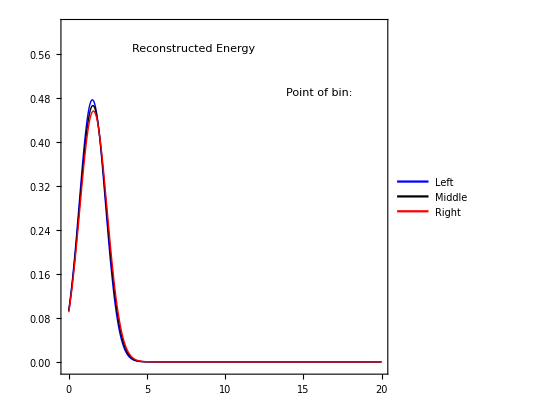

```mathematica
Clear[n,FcutE1,FcutE2,FcutE3]

n=1;  (* n-th bin_true *)
EnTrue = 3.25+(n-1)*0.5;
{ {" n-th(true)", " En_true(middle) "},{" : "},{ n ,3.25+(n-1)*0.5 } }


(* Calculate of Gassian for first bin_true (not null): Left/Middle/Right *)
(* OBS: En(true)_lim ≳ 3.35 *)
	FcutE1[y_] := Fcut[y,3.35]                              (* Left_bin (true) *)
	FcutE2[y_] := Fcut[y,(3.35+3.5)/2]         (* Middle_bin (true) *)
	FcutE3[y_] := Fcut[y,3.5]                                (* Right_bin (true) *)


Plot[  { FcutE1[Ereco],FcutE2[Ereco],FcutE3[Ereco] },{Ereco,0,20},PlotRange->{{-0.1,20},{-0.01,0.61}}, 
	AspectRatio->1, Frame->True,FrameStyle->Thickness[0.006],LabelStyle->{FontSize->15},
	Epilog->
		{
		Text["Reconstructed Energy",{8,0.57},BaseStyle->{FontSize->22,FontFamily->"Arial",FontWeight->"Bold"}],
		Text["Point of bin:",{16,0.49},BaseStyle->{FontSize->16,FontFamily->"Arial",FontWeight->"Bold"}]
		},
	PlotStyle->{Directive[Thick,Blue],Directive[Thick,Black],Directive[Thick,Red]},
	PlotLegends ->Placed[{"Left","Middle","Right"},{Scaled[{0.9,0.78}],{1,1}}],
	ImageSize->410 ]
```

Calculation of reconstruction energy per bin

```mathematica
Clear[m, EnReco]
m =4; (* m-th bin_reconstructed *)
EnReco = 0.25 + (m-1)*0.5;
{ {" m-th(reco)", " En_reco(middle) "},{" : "},{ m ,EnReco } }

(* Average True *)
	{ 
	SomaE1=Divide[#,3]&@Total[ { FcutE1[Ereco],FcutE2[Ereco],FcutE3[Ereco] } ]/.Ereco->EnReco-0.5/2,
	SomaE2=Divide[#,3]&@Total[ { FcutE1[Ereco],FcutE2[Ereco],FcutE3[Ereco] } ]/.Ereco->EnReco,
	SomaE3=Divide[#,3]&@Total[ { FcutE1[Ereco],FcutE2[Ereco],FcutE3[Ereco] } ]/.Ereco->EnReco+0.5/2
	}


Print["Reconstructed with average in E_true and E_reco: ",Total[ { SomaE1,SomaE2,SomaE3 } ]/3   ]
Print["Reconstructed with average only in E_true: ",( Total[ { FcutE1[Ereco],FcutE2[Ereco],FcutE3[Ereco] } ]/.Ereco->EnReco )/3,  "\n"  ]

{FuncGassian[EnReco-0.5/2,EnTrue],FuncGassian[EnReco,EnTrue],FuncGassian[EnReco+0.5/2,EnTrue] }
Print["Reconstructed with average only in E_reco: ",( FuncGassian[EnReco-0.5/2,EnTrue]+FuncGassian[EnReco,EnTrue]+FuncGassian[EnReco+0.5/2,EnTrue] )/3 ]
Print["Not considering the average in any way: ",FuncGassian[Ereco,EnTrue]/.Ereco->EnReco]
```

{{ m-th(reco), En_reco(middle) },{ : },{4,1.75}}

{0.465323,0.451992,0.40318}

Reconstructed with average in E_true and E_reco: 0.440165

Reconstructed with average only in E_true: 0.451992

{0.490483,0.46121,0.394508}

Reconstructed with average only in E_reco: 0.448734

Not considering the average in any way: 0.46121

### For n-th bin_true, except the first ( Obs: bin_true not null ):

{{ n-th(true), En_true(middle) },{ : },{2,3.75}}

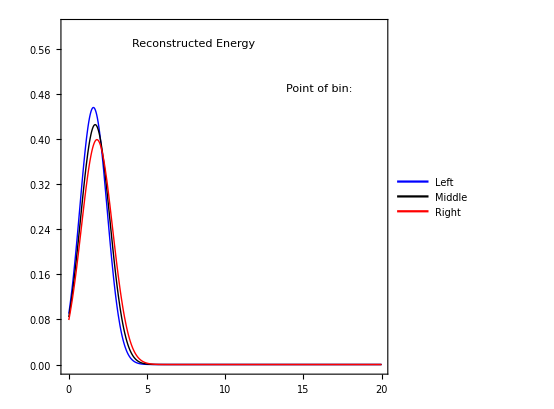

```mathematica
Clear[n,FcutLef,FcutMid,FcutRig]

n=2;  (* n-th bin_true *)
EnTrue = 3.25+(n-1)*0.5;
{ {" n-th(true)", " En_true(middle) "},{" : "},{ n ,3.25+(n-1)*0.5 } }


(* Calculate of Gassian bin_true (not null): Left/Middle/Right *)
	FcutLef[y_] := Fcut[y,3.0+(n-1)*0.5]                    (* Left_bin (true) *)
	FcutMid[y_] := Fcut[y,3.25+(n-1)*0.5]                  (* Middle_bin (true) *)
	FcutRig[y_] := Fcut[y,3.5+(n-1)*0.5]                    (* Right_bin (true) *)


Plot[  { FcutLef[Ereco],FcutMid[Ereco],FcutRig[Ereco] },{Ereco,0,20},PlotRange->{{-0.1,20},{-0.005,0.6}}, 
	AspectRatio->1, Frame->True,FrameStyle->Thickness[0.006],LabelStyle->{FontSize->15},
	Epilog->
		{
		Text["Reconstructed Energy",{8,0.57},BaseStyle->{FontSize->22,FontFamily->"Arial",FontWeight->"Bold"}],
		Text["Point of bin:",{16,0.49},BaseStyle->{FontSize->16,FontFamily->"Arial",FontWeight->"Bold"}]
		},
	PlotStyle->{Directive[Thick,Blue],Directive[Thick,Black],Directive[Thick,Red]},
	PlotLegends ->Placed[{"Left","Middle","Right"},{Scaled[{0.9,0.78}],{1,1}}],
	ImageSize->410 ]
```

Calculation of reconstruction energy per bin

```mathematica
Clear[m, EnReco]
m =4; (* m-th bin_reconstructed *)
EnReco = 0.25 + (m-1)*0.5;
{ {" m-th(reco)", " En_reco(middle) "},{" : "},{ m ,EnReco } }

(* Average True *)
	{ 
	SomaLef=Divide[#,3]&@Total[ { FcutLef[Ereco],FcutMid[Ereco],FcutRig[Ereco] } ]/.Ereco->EnReco-0.5/2,
	SomaMid=Divide[#,3]&@Total[ { FcutLef[Ereco],FcutMid[Ereco],FcutRig[Ereco] } ]/.Ereco->EnReco,
	SomaRig=Divide[#,3]&@Total[ { FcutLef[Ereco],FcutMid[Ereco],FcutRig[Ereco] } ]/.Ereco->EnReco+0.5/2
	}


Print["Reconstructed with average in E_true and E_reco: ",Total[ { SomaLef,SomaMid,SomaRig } ]/3   ]
Print["Reconstructed with average only in E_true: ",(Total[{FcutLef[Ereco],FcutMid[Ereco],FcutRig[Ereco]}]/.Ereco->EnReco)/3,  "\n"  ]

{ Fcut[EnReco-0.5/2,EnTrue],Fcut[EnReco,EnTrue],Fcut[EnReco+0.5/2,EnTrue] }
Print["Reconstructed with average only in E_reco: ",( Fcut[EnReco-0.5/2,EnTrue]+Fcut[EnReco,EnTrue]+Fcut[EnReco+0.5/2,EnTrue] )/3 ]
Print["Not considering the average in any way: ",FuncGassian[Ereco,EnTrue]/.Ereco->EnReco]
```

{{ m-th(reco), En_reco(middle) },{ : },{4,1.75}}

{0.417587,0.423315,0.399596}

Reconstructed with average in E_true and E_reco: 0.413499

Reconstructed with average only in E_true: 0.423315

{0.417112,0.424594,0.402542}

Reconstructed with average only in E_reco: 0.414749

Not considering the average in any way: 0.424594